Абсолютная точность Рунге-Кутты

0.121602

0.0807417

0.0833107

0.0878146

Оценка погрешности метода Рунге-Кутты методом Рунге

5.82235

4.61183

4.6501

4.75467

График сходимости

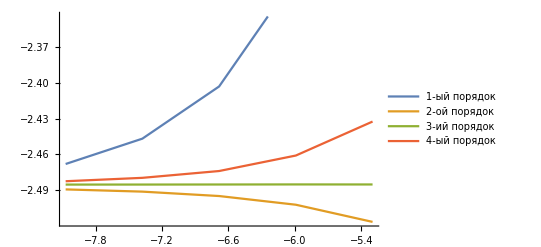

График решения (Метод:Рунге)

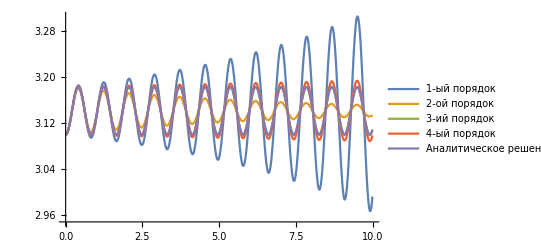

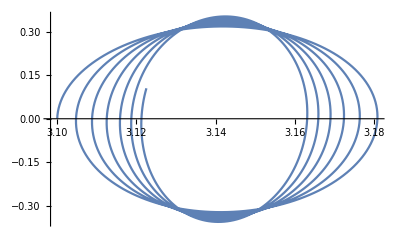

Условие устойчивости НЕ ВЫПОЛНЕНО

```mathematica
SMassiv1=ReadList["C:\\repos\\python\\CHM-2\\Lab2_again\\runge-order1.txt" ]; (* тут читаются листы*)
SMassiv2=ReadList["C:\\repos\\python\\CHM-2\\Lab2_again\\runge-order2.txt" ];
SMassiv3=ReadList["C:\\repos\\python\\CHM-2\\Lab2_again\\runge-order3.txt" ];
SMassiv4=ReadList["C:\\repos\\python\\CHM-2\\Lab2_again\\runge-order4.txt" ];

Massiv1=ToExpression[SMassiv1][[1]];(*Решение 1 порядок*)
Massiv2=ToExpression[SMassiv2][[1]];(*Решение 2 порядок*)
Massiv3=ToExpression[SMassiv3][[1]];(*Решение 3 порядок*)
Massiv4=ToExpression[SMassiv4][[1]];(*Решение 4 порядок*)
Temp=NDSolve[{y''[x]== (3/(2*10))*(386 - 0.5*5.3*Sin[5.3*x])*Sin[y[x]],y[0]==3.1,y'[0]==0},y,{x,0,10}];
Massiv =Table[{x,Evaluate[y[x]/.Temp][[1]]},{x,0,10,0.01}];(*Точное решение*)
(*Точность решения 1*)
Print["Абсолютная точность Рунге-Кутты"];
MAX1 = Max[Table[Abs[Massiv[[i,2]]-Massiv1[[i,2]]],{i, 1, 1000}]](*Точность решения (Метод:Рунге)*)
MAX2 = Max[Table[Abs[Massiv[[i,2]]-Massiv2[[i,2]]],{i, 1, 1000}]](*Точность решения (Метод:Рунге)*)
MAX3 = Max[Table[Abs[Massiv[[i,2]]-Massiv3[[i,2]]],{i, 1, 1000}]](*Точность решения (Метод:Рунге)*)
MAX4 = Max[Table[Abs[Massiv[[i,2]]-Massiv4[[i,2]]],{i, 1, 1000}]](*Точность решения (Метод:Рунге)*)
(*Оценка погрешности*)
P1=2;

SMassiv11=ReadList["C:\\repos\\python\\CHM-2\\Lab2_again\\runge-order1-1.txt" ];
SMassiv22=ReadList["C:\\repos\\python\\CHM-2\\Lab2_again\\runge-order2-1.txt" ];
SMassiv33=ReadList["C:\\repos\\python\\CHM-2\\Lab2_again\\runge-order3-1.txt" ];
SMassiv44=ReadList["C:\\repos\\python\\CHM-2\\Lab2_again\\runge-order4-1.txt" ];
Massiv11=ToExpression[SMassiv11][[1]];(*Рунге-Кутты*)
Massiv22=ToExpression[SMassiv22][[1]];(*Рунге-Кутты*)
Massiv33=ToExpression[SMassiv33][[1]];(*Рунге-Кутты*)
Massiv44=ToExpression[SMassiv44][[1]];(*Рунге-Кутты*)
Print["Оценка погрешности метода Рунге-Кутты методом Рунге "];
MAX11 = Max[Table[Abs[(2^P1/(2^P1-1))(Massiv11[[2i,2]]-Massiv1[[i,2]])],{i, 1, 1000}]]
MAX22 = Max[Table[Abs[(2^P1/(2^P1-1))(Massiv22[[2i,2]]-Massiv2[[i,2]])],{i, 1, 1000}]]
MAX33 = Max[Table[Abs[(2^P1/(2^P1-1))(Massiv33[[2i,2]]-Massiv3[[i,2]])],{i, 1, 1000}]]
MAX44 = Max[Table[Abs[(2^P1/(2^P1-1))(Massiv44[[2i,2]]-Massiv4[[i,2]])],{i, 1, 1000}]](*Точность решения (Метод:Рунге)*)
(*Сходимость*)
SMoreMassiv1=ReadList["C:\\repos\\python\\CHM-2\\Lab2_again\\all-runge-order1.txt"  ];
SMoreMassiv2=ReadList["C:\\repos\\python\\CHM-2\\Lab2_again\\all-runge-order2.txt"  ];
SMoreMassiv3=ReadList["C:\\repos\\python\\CHM-2\\Lab2_again\\all-runge-order3.txt"  ];
SMoreMassiv4=ReadList["C:\\repos\\python\\CHM-2\\Lab2_again\\all-runge-order4.txt"  ];
MoreMassiv1=ToExpression[SMoreMassiv1];(*Рунге-Кутты*)
MoreMassiv2=ToExpression[SMoreMassiv2];(*Рунге-Кутты*)
MoreMassiv3=ToExpression[SMoreMassiv3];(*Рунге-Кутты*)
MoreMassiv4=ToExpression[SMoreMassiv4];(*Рунге-Кутты*)
Graph1 = 
Table[{Log[MoreMassiv1[[k,2,1]]],
Log[Max[Table[Abs[(Massiv[[i,2]]-MoreMassiv1[[k,2^(k-1) i,2]])],{i, 1, 1000}]]]},{k,1,5}];
Graph2 = Table[{Log[MoreMassiv2[[k,2,1]]],Log[Max[Table[Abs[(Massiv[[i,2]]-MoreMassiv2[[k,2^(k-1) i,2]])],{i, 1, 1000}]]]},{k,1,5}];
Graph3 = Table[{Log[MoreMassiv3[[k,2,1]]],Log[Max[Table[Abs[(Massiv[[i,2]]-MoreMassiv3[[k,2^(k-1) i,2]])],{i, 1, 1000}]]]},{k,1,5}];
Graph4 = Table[{Log[MoreMassiv4[[k,2,1]]],Log[Max[Table[Abs[(Massiv[[i,2]]-MoreMassiv4[[k,2^(k-1) i,2]])],{i, 1, 1000}]]]},{k,1,5}];
Print["График сходимости"]
ListLinePlot[{Graph1,Graph2, Graph3,Graph4}, PlotLegends->{"1-ый порядок", "2-ой порядок", "3-ий порядок", "4-ый порядок"}]
Print["График решения (Метод:Рунге)"]
ListLinePlot[{Massiv1,Massiv2, Massiv3, Massiv4, Massiv}, PlotLegends->{"1-ый порядок", "2-ой порядок", "3-ий порядок", "4-ый порядок", "Аналитическое решение"}]
SMoreMassiv2=ReadList["C:\\repos\\python\\CHM-2\\Lab2_again\\runge-order4-1.txt"];
DyMassiv2=ToExpression[SMoreMassiv2][[1]];(*Рунге-Кутты*)
FazT2= Table[{Massiv2[[i,2]],DyMassiv2[[i,2]]},{i,1,1000}];
ListLinePlot[FazT2]
If[ Min[Table[DyMassiv2[[i,2]],{i,1,1000}]]<0,Print["Условие устойчивости НЕ ВЫПОЛНЕНО"], Print["Условие устойчивости ВЫПОЛНЕНО"]]
```